# NEAT

студент 3 курса 5 группы
Лицкевич Данила
20-12-2020

# NEAT

## 0. Info

https://towardsdatascience.com/neat-an-awesome-approach-to-neuroevolution-3eca5cc7930f

## 1. Individuals

## Generating Population

### Nodes

#### kmActivationFunc

```mathematica
kmActivationFunc[id_]:=
Switch[id,
0, #&,
1,Tanh[#]&,
2,LogisticSigmoid[#]&,
3,Sin[#]&,
4,UnitStep[#]&,
5,Ramp[#]&
]
```

#### kmNode

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
ClearAll[kmNode]
kmNode[id_,layer_,func_:False,totalFuncs_:5]:=<|
"nodeId"->id,
"layer"->layer,
"inputSum"->0,
"bias"->RandomReal[{-2,2}],
"activationFunc"->If[func===False,RandomInteger[totalFuncs],func],
"output"->0
|>
```

```mathematica
ClearAll[kmNodeOutput]
kmNodeOutput[node_,prevNodes_]:=
Join[node,<|"inputSum"->#,"output"->node["bias"]+kmActivationFunc[node["activationFunc"]][#]|>]&[Total[prevNodes⟦All,"output"⟧]]
```

```mathematica
kmNode[1,1]
kmNodeOutput[%,{kmNode[2,1]~Join~<|"output"->12|>,kmNode[3,2]~Join~<|"output"->2|>}]
```

<|nodeId→1,layer→1,inputSum→0,bias→0.600685,activationFunc→0,output→0|>

<|nodeId→1,layer→1,inputSum→14,bias→0.600685,activationFunc→0,output→14.6007|>

```mathematica
kmNodeOutput[kmNode[1,1],{}]
```

<|nodeId→1,layer→1,inputSum→0,bias→-0.196276,activationFunc→0,output→-0.196276|>

### Connections

```mathematica
CantorPairing[x_,y_]:=((x+y)(x+y+1))/2+y
```

#### kmConnection

Input — нейрон входа ;
Output — нейрон выхода;
weight — вес скрытых нейронов ;
enabled — активирована ли связь;
inovation — появление ;

```mathematica
kmConnection[{in_,out_},weight_:1]:=<|
"input"->in,
"output"->out,
"weight"->RandomReal[{-weight,weight}],
"enabled"->True,
"inovation"->CantorPairing[in,out]
|>
```

### Individual

Input and output nodes are not evolved in the node gene list. Hidden nodes can be added or removed.

```mathematica
ClearAll[kmIndividual]
kmIndividual[input_,output_,hidden_:0]:=
<|
"input"->input,
"output"->output,
"total"->input+output,
"fitness"->∞,
"nodes"->Join[
kmNode[#,1,0]&/@Range[input],
kmNode[#,2]&/@(input+Range[output])
],
"connections"->(kmConnection[#]&/@
Flatten[
Outer[
{#1,#2}&,
Range[input],
Range[input+1,input+output]
],1])
|>
```

### Population

Input — количество входов;
Output — количество выходов;

```mathematica
kmPopulation[in_,out_,size_:10,options___]:=<|
"input"->in,
"output"->out,
"best"-><|"fitness"->+∞|>,
"history"->{},
"size"->size,
(*"inovations"->{},*)
"individuals"->Array[kmIndividual[in,out]&,size],
"state"->{0,0,0},
"params"-><|
"updNodeRate"->0.8,
"updConnRate"->0.2,
"addConnRate"->0.95,
"removeConnRate"->0.1,
"addNodeRate"->0.001,
"removeNodeRate"->0.05,
"crossOverRate"->0.24
|>
|>~Join~options
```

### Tests

```mathematica
testPop=kmPopulation[2,3];
```

## Individual decoding

### Connection' s logics

#### kmFindNode

```mathematica
kmFindNode[individual_,id_]:=
First@FirstPosition[individual["nodes"],<|"nodeId"->id,___|>]
```

```mathematica
kmFindNode[testPop["individuals"]⟦1⟧,3]
```

3

#### kmInNodes

Finds all nodes which are  IN nodes for the node

```mathematica
kmInNodes[nodeId_,connections_]:=
Reap[
If[nodeId==#["output"],Sow[#["input"]]]&/@connections;
]//Last//Flatten
```

```mathematica
kmInNodes[2,{kmConnection[{1,2}],kmConnection[{3,2}]}]
```

{1,3}

#### kmExistConnectionQ

```mathematica
kmExistConnectionQ[connection:{in_,out_},connections_]:= 
Or@@({#["input"],#["output"]}==connection&/@connections)
```

### Prepare for evaluation

#### kmNodesToLayers

```mathematica
ClearAll[kmNodesToLayers]
kmNodesToLayers[individual_]:=
Module[
{maxLayer=Max[individual[["nodes",All,"layer"]]],
nodes
},
Join[individual,
<|
"maxLayer"->maxLayer,
"nodesLayered"->(Function[{layer},Select[individual["nodes"],#["layer"]==layer&]]/@Range[maxLayer])
|>
]
]
```

#### kmIndividualsToLayers

```mathematica
ClearAll[kmIndividualsPrepare]
SetAttributes[kmIndividualsPrepare,HoldFirst]
kmIndividualsPrepare[population_]:=
population⟦"individuals"⟧=kmNodesToLayers[#]&/@population["individuals"]
```

```mathematica
kmIndividualsPrepare[testPop];
```

#### kmGetNodesLayered

```mathematica
ClearAll[kmGetNodesLayered]
kmGetNodesLayered[individual_,nodeIds_]:=
Flatten[Function[{nodeId},Select[individual["nodesLayered"]//Flatten,#["nodeId"]==nodeId&,1]]/@nodeIds]
```

#### kmInNodesLayered

```mathematica
ClearAll[kmInNodesLayered]
kmInNodesLayered[individual_,node_]:=kmGetNodesLayered[individual,kmInNodes[node["nodeId"],individual["connections"]]]
```

```mathematica
kmInNodesLayered[testPop["individuals"][[1]],<|"nodeId"->3,"layer"->1,"inputSum"->0,"bias"->-0.012840107337042994,"activationFunc"->0,"output"->1|>]
```

{<|nodeId→1,layer→1,inputSum→0,bias→0.526354,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.8927,activationFunc→0,output→0|>}

### Evaluation

#### kmInitFirstLayer

```mathematica
ClearAll[kmInitFirstLayer]
kmInitFirstLayer[nodes_,inputs_List]:=
MapThread[Join[#1,<|"output"->#2|>]&,{SortBy[Take[nodes,Length[inputs]],#["nodeId"]&],inputs}]
```

#### kmIndividualEvaluate

```mathematica
ClearAll[kmIndividualEvaluate]
kmIndividualEvaluate[individual_,inputs_:{_,_}]:=
Module[
{individualCopy=individual},

individualCopy[["nodesLayered",1]]=kmInitFirstLayer[individualCopy["nodesLayered"]//First,inputs];
Function[{layer},
individualCopy[["nodesLayered",layer]]=
Function[{node},
kmNodeOutput[node,kmInNodesLayered[individualCopy,node]]
]/@individualCopy[["nodesLayered",layer]]
]/@Range[2,individual["maxLayer"]];
kmGetNodesLayered[individualCopy,Range[#+1,#+individual["output"]]&[individual["input"]]]⟦All,"output"⟧
]
```

```mathematica
kmIndividualEvaluate[popClassTest["individuals"][[9]],{.1,.2}]
```

{-0.163402}

## Population viewing (realisatoin Delayed)

```mathematica
testIndividual=<|"input"->2,"output"->3,"hidden"->4,"connections"->{<|"input"->1,"output"->5,"weight"->-0.9628618224751473,"enabled"->1,"inovation"->1|>,<|"input"->3,"output"->4,"weight"->0.22393191857363837,"enabled"->1,"inovation"->2|>,<|"input"->4,"output"->6,"weight"->-0.4785485230617863,"enabled"->1,"inovation"->3|>,<|"input"->6,"output"->5,"weight"->0.45075859641862426,"enabled"->1,"inovation"->4|>,<|"input"->8,"output"->5,"weight"->0.5039873848534051,"enabled"->1,"inovation"->5|>}|>;
```

### Individual viewing

#### kmNodes

1  – in node
2  – out node
3  – hidden node

```mathematica
kmNodes[type_,nodesQuant_,layer_]:=
{Switch[type,1,Red,2,Blue,3,Gray,True,Black],Disk[{-nodesQuant+2#,layer},0.25]&/@Range[nodesQuant]}
```

#### kmViewIndividual

```mathematica
kmViewIndividual[individ_]:=
Graphics[{kmNodes[1,3,1],kmNodes[2,2,2]}]
```

```mathematica
Dynamic@kmViewIndividual[1]
```

```mathematica
Graph
```

Graph

### Population viewing

## Population operations

### kmAddConnection

```mathematica
SetAttributes[kmAddConnection,HoldFirst]
kmAddConnection[population_,individualId_,conn:{in_,out_}]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
existId=Position[population[["individuals",individualId,"connections"]],_?(#["input"]==in&&#["output"]==out&)]
},
If[Length[existId]==0,
individual⟦"connections"⟧=Join[
individual["connections"],
If[individual["nodes"]⟦kmFindNode[individual,in],"layer"⟧<individual["nodes"]⟦kmFindNode[individual,out],"layer"⟧,{kmConnection[conn]},{}]
];,
individual⟦"connections",existId//Last⟧=kmConnection[conn]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

### kmAddNode

```mathematica
SetAttributes[kmAddNode,HoldFirst]
kmAddNode[population_,individualId_,connectionId_]:= 
Block[{
individual=population["individuals"]⟦individualId⟧,
connection, oldOutNodePos
},
connection=individual["connections"]⟦connectionId⟧;
individual⟦"connections",connectionId,"enabled"⟧=False;

oldOutNodePos=kmFindNode[individual,connection["output"]];
individual⟦"total"⟧+=1;
individual⟦"nodes"⟧=
Append[individual["nodes"],kmNode[individual["total"],individual⟦"nodes",oldOutNodePos,"layer"⟧]];
individual⟦"nodes",oldOutNodePos,"layer"⟧+=1;

individual⟦"connections"⟧=Join[
{kmConnection[{connection["input"],#}],
kmConnection[{#,connection["output"]}]}&[individual["total"]],
individual["connections"]
];
population⟦"individuals", individualId⟧=kmNodesToLayers[individual]
]
```

```mathematica
popClassTest[["individuals",4]]
```

<|input→2,output→1,total→3,fitness→2.96833,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.347333,activationFunc→0,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→-0.926786,activationFunc→3,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.160061,activationFunc→0,output→0|>},connections→{<|input→1,output→3,weight→-0.0355081,enabled→True,inovation→13|>,<|input→2,output→3,weight→0.123903,enabled→True,inovation→18|>},maxLayer→2,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.347333,activationFunc→0,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.160061,activationFunc→0,output→0|>},{<|nodeId→3,layer→2,inputSum→0,bias→-0.926786,activationFunc→3,output→0|>}}|>

```mathematica
Position[testPop[["individuals",1,"connections"]],_?(#["input"]==1&&#["output"]==3&)]//Length
```

Last[{}]

```mathematica
testPop[["individuals",1,"connections",{1}]]
```

{<|input→1,output→6,weight→0.729431,enabled→True,inovation→34|>}

```mathematica
testPop[["individuals",1,"connections"]]
```

{<|input→1,output→6,weight→0.729431,enabled→True,inovation→34|>,<|input→6,output→3,weight→0.325952,enabled→True,inovation→48|>,<|input→1,output→3,weight→-0.795041,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.112627,enabled→True,inovation→19|>,<|input→1,output→5,weight→0.463564,enabled→True,inovation→26|>,<|input→2,output→3,weight→0.993449,enabled→True,inovation→18|>,<|input→2,output→4,weight→0.841671,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.88586,enabled→True,inovation→33|>,<|input→1,output→6,weight→0.543443,enabled→True,inovation→34|>,<|input→1,output→6,weight→0.579967,enabled→True,inovation→34|>}

### tests

```mathematica
kmAddNode[testPop,1,1]
kmAddConnection[testPop,1,{1,6}]
```

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.707313,activationFunc→0,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.114648,activationFunc→4,output→0|>},connections→{<|input→1,output→6,weight→0.803674,enabled→True,inovation→34|>,<|input→6,output→3,weight→-0.788148,enabled→True,inovation→48|>,<|input→1,output→3,weight→0.218483,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.301039,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.5069,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.743409,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.765708,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.247678,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.114648,activationFunc→4,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.707313,activationFunc→0,output→0|>}}|>

<|input→2,output→3,total→6,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>,<|nodeId→3,layer→3,inputSum→0,bias→0.707313,activationFunc→0,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.114648,activationFunc→4,output→0|>},connections→{<|input→1,output→6,weight→-0.112103,enabled→True,inovation→34|>,<|input→6,output→3,weight→-0.788148,enabled→True,inovation→48|>,<|input→1,output→3,weight→0.218483,enabled→False,inovation→13|>,<|input→1,output→4,weight→0.301039,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.5069,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.743409,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.765708,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.247678,enabled→True,inovation→33|>},maxLayer→3,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>,<|nodeId→6,layer→2,inputSum→0,bias→0.114648,activationFunc→4,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.707313,activationFunc→0,output→0|>}}|>

## Population mutations

#### kmUpdateNode

```mathematica
ClearAll[kmUpdateNode]
SetAttributes[kmUpdateNode,HoldFirst]
kmUpdateNode[population_,individualId_,nodeId_]:= 
If[
RandomReal[]<population["params","updNodeRate"],
population["state"]=population["state"]+{0,1,0};
population[["individuals",individualId,"nodes",nodeId]]=If[RandomReal[]<0.75,kmNode[#["nodeId"],#["layer"],#["activationFunc"]],kmNode[#["nodeId"],#["layer"]]]
&[population[["individuals",individualId,"nodes",nodeId]]]
]
```

### kmMutateNodes

```mathematica
ClearAll[kmMutateNodes]
SetAttributes[kmMutateNodes,HoldFirst]
kmMutateNodes[population_,individualId_]:= 
If[
RandomReal[]<population["params","addNodeRate"],
population["state"]=population["state"]+{0,10000,0};
kmAddNode[population,individualId,RandomInteger[{1,Length[population⟦"individuals",individualId,"connections"⟧]}]],
Do[kmUpdateNode[population,individualId,RandomInteger[{1,population[["individuals",individualId,"total"]]}]],3];
population[["individuals",individualId]]=kmNodesToLayers@population[["individuals",individualId]]
]
```

```mathematica
kmMutateNodes[testPop,1]
```

<|input→2,output→3,total→5,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>,<|nodeId→3,layer→2,inputSum→0,bias→0.707313,activationFunc→0,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>},connections→{<|input→1,output→3,weight→0.218483,enabled→True,inovation→13|>,<|input→1,output→4,weight→0.301039,enabled→True,inovation→19|>,<|input→1,output→5,weight→-0.5069,enabled→True,inovation→26|>,<|input→2,output→3,weight→-0.743409,enabled→True,inovation→18|>,<|input→2,output→4,weight→-0.765708,enabled→True,inovation→25|>,<|input→2,output→5,weight→-0.247678,enabled→True,inovation→33|>},maxLayer→2,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→0.444852,activationFunc→1,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.594565,activationFunc→1,output→0|>},{<|nodeId→3,layer→2,inputSum→0,bias→0.707313,activationFunc→0,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.545397,activationFunc→3,output→0|>,<|nodeId→5,layer→2,inputSum→0,bias→-0.476285,activationFunc→1,output→0|>}}|>

### kmMutateConnections

```mathematica
ClearAll[kmMutateConnections]
SetAttributes[kmMutateConnections,HoldFirst]
kmMutateConnections[population_,individualId_]:= 
Which[
RandomReal[]<population["params","addConnRate"],
population["state"]=population["state"]+{0,0,1};
kmAddConnection[population,individualId,RandomSample[population[["individuals",individualId,"nodes"]],2]⟦All,"nodeId"⟧],
population[["individuals",individualId]]
]
```

### kmCrossover

#### kmNodesFromConns

```mathematica
kmNodesFromConnections[connections_]:= 
Union[Part[connections,All,"input"],Part[connections,All,"output"]]
```

#### kmCrossover

```mathematica
ClearAll[kmCrossover]
kmCrossover[posParent1_,posParent2_]:= 
Module[
{conns1,conns2, nodes1Ids,nodes2, 
parent1,parent2,
separator= RandomChoice[
Join[posParent1["connections"],posParent2["connections"]]
]["inovation"]
},
{parent1,parent2}=RandomSample[{posParent1,posParent2}];
conns1 =Select[parent1["connections"],#["inovation"]≤separator&] ;
conns2=Select[parent2["connections"],#["inovation"]>separator&];
nodes1Ids=kmNodesFromConnections[conns1];
nodes2=Select[parent2["nodes"],!MemberQ[parent1["nodes"]⟦nodes1Ids⟧⟦All,"nodeId"⟧,#["nodeId"]]&];
(*Print[{nodes1Ids,nodes2}];*)
kmNodesToLayers@<|
"input"->parent1["input"],
"output"->parent1["output"],
"total"->Length[Join[nodes1Ids,nodes2]],
"fitness"->∞,
"nodes"->Join[parent1["nodes"]⟦nodes1Ids⟧,nodes2],
"connections"->Join[conns1,conns2]
|>
]
```

```mathematica
kmCrossover[popClassTest[["individuals",14]],popClassTest[["individuals",#]]]&/@Range[3,20];
%[[All,"nodesLayered"]]
```

{{{<|nodeId→1,layer→1,inputSum→0,bias→0.565756,activationFunc→1,output→0|>},{<|nodeId→2,layer→2,inputSum→0,bias→0.170445,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.274045,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.436812,activationFunc→3,output→0|>,<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.464903,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→0.924612,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.240045,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.464903,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→0.924612,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.346994,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.65471,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→-0.236836,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→0.547196,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.624599,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.457581,activationFunc→5,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.248824,activationFunc→3,output→0|>,<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.944275,activationFunc→1,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→0.0626761,activationFunc→2,output→0|>},{<|nodeId→2,layer→2,inputSum→0,bias→0.170445,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.00214951,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.436812,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.346994,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.65471,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.809945,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→-0.236836,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→0.553496,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→0.718325,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→-0.488032,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.457581,activationFunc→5,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→0.481327,activationFunc→3,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.384582,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.163101,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→0.277768,activationFunc→3,output→0|>,<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.768963,activationFunc→2,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.19086,activationFunc→1,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→0.0626761,activationFunc→2,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→-0.274045,activationFunc→2,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}},{{<|nodeId→1,layer→1,inputSum→0,bias→0.547196,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.376772,activationFunc→1,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.153951,activationFunc→2,output→0|>},{<|nodeId→3,layer→3,inputSum→0,bias→-0.532131,activationFunc→3,output→0|>,<|nodeId→5,layer→3,inputSum→0,bias→-0.598303,activationFunc→4,output→0|>}}}

```mathematica
kmCrossover[popClassTest[["individuals",14]],popClassTest[["individuals",3]]]
```

{{1,2},{<|nodeId→2,layer→2,inputSum→0,bias→0.170445,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.274045,activationFunc→2,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→-0.916664,activationFunc→2,output→0|>}}

<|input→2,output→1,total→5,fitness→∞,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>,<|nodeId→2,layer→2,inputSum→0,bias→0.170445,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.274045,activationFunc→2,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→-0.916664,activationFunc→2,output→0|>},connections→{<|input→1,output→2,weight→-0.588869,enabled→True,inovation→8|>,<|input→1,output→5,weight→-0.62296,enabled→True,inovation→26|>,<|input→5,output→2,weight→0.0676681,enabled→True,inovation→30|>,<|input→1,output→3,weight→-0.218506,enabled→True,inovation→13|>,<|input→3,output→2,weight→-0.527352,enabled→True,inovation→17|>,<|input→1,output→4,weight→0.269558,enabled→True,inovation→19|>,<|input→2,output→3,weight→-0.621896,enabled→True,inovation→18|>,<|input→4,output→3,weight→-0.305682,enabled→True,inovation→31|>,<|input→3,output→4,weight→-0.509835,enabled→True,inovation→32|>,<|input→4,output→2,weight→0.619725,enabled→True,inovation→23|>},maxLayer→4,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→-0.916664,activationFunc→2,output→0|>},{<|nodeId→2,layer→2,inputSum→0,bias→0.170445,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→-0.274045,activationFunc→2,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→0.531879,activationFunc→3,output→0|>}}|>

```mathematica
popClassTest[["individuals",1]]
```

<|input→2,output→1,total→5,fitness→3.207,nodes→{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→3,layer→4,inputSum→0,bias→-0.777058,activationFunc→3,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.0159173,activationFunc→1,output→0|>,<|nodeId→4,layer→2,inputSum→0,bias→0.193825,activationFunc→2,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→-0.916664,activationFunc→2,output→0|>},connections→{<|input→1,output→2,weight→-0.753012,enabled→True,inovation→8|>,<|input→1,output→3,weight→-0.218506,enabled→True,inovation→13|>,<|input→3,output→2,weight→0.510992,enabled→True,inovation→17|>,<|input→1,output→4,weight→-0.757541,enabled→True,inovation→19|>,<|input→2,output→3,weight→-0.376405,enabled→True,inovation→18|>,<|input→1,output→5,weight→-0.62296,enabled→True,inovation→26|>,<|input→5,output→2,weight→0.0676681,enabled→True,inovation→30|>,<|input→4,output→3,weight→-0.305682,enabled→True,inovation→31|>,<|input→3,output→4,weight→-0.509835,enabled→True,inovation→32|>,<|input→4,output→2,weight→0.619725,enabled→True,inovation→23|>},maxLayer→4,nodesLayered→{{<|nodeId→1,layer→1,inputSum→0,bias→-0.958617,activationFunc→5,output→0|>,<|nodeId→2,layer→1,inputSum→0,bias→-0.0159173,activationFunc→1,output→0|>,<|nodeId→5,layer→1,inputSum→0,bias→-0.916664,activationFunc→2,output→0|>},{<|nodeId→4,layer→2,inputSum→0,bias→0.193825,activationFunc→2,output→0|>},{},{<|nodeId→3,layer→4,inputSum→0,bias→-0.777058,activationFunc→3,output→0|>}}|>

## Population evolution

### Fitness

#### kmAssessFitnessAll

```mathematica
ClearAll[kmAssessFitnessAll]
SetAttributes[kmAssessFitnessAll,HoldFirst]
kmAssessFitnessAll[population_Symbol,fitness_Function]:=Module[
{min},
min=Min[population[["individuals",All,"fitness"]]=(fitness/@population["individuals"])];

If[min<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",Position[population[["individuals",All,"fitness"]],min]⟦1,1⟧⟧
]
]
]
```

#### kmAssessFitness

```mathematica
ClearAll[kmAssessFitness]
SetAttributes[kmAssessFitness,HoldFirst]
kmAssessFitness[population_Symbol,fitness_Function,individualId_]:=Module[
{fit},
fit=population[["individuals",individualId,"fitness"]]=fitness@population[["individuals",individualId]];
If[fit<population["best","fitness"],
AppendTo[population["history"],
population["best"]=population⟦"individuals",individualId⟧
]
]
]
```

### Elimination

```mathematica
SetAttributes[kmElimination,HoldFirst]
kmElimination[population_,replaceIndividual_]:=
Block[{
index=RandomChoice[(Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
},
(*Print[index];*)
population⟦"individuals",index⟧=replaceIndividual;
index
]
```

### Selection

```mathematica
SetAttributes[kmSelection,HoldFirst]
kmSelection[population_]:=
RandomChoice[(#/Total[#]&)@(1/Exp/@population[["individuals",All,"fitness"]])->Range[population["size"]]]
```

### Evolution

```mathematica
ClearAll[kmEvolveOne]
SetAttributes[kmEvolveOne,HoldFirst]
kmEvolveOne[population_,fitness_]:=
Catch[
Block[{individualId=kmSelection[population]},
(*kmAssessFitness[population,fitness];*)
Which[
RandomReal[]<population⟦"params","crossOverRate"⟧,
population["state"]=population["state"]+{1,0,0};
kmAssessFitness[population,fitness,kmElimination[population,#]]&[
kmCrossover[population⟦"individuals",individualId⟧,
population⟦"individuals",RandomInteger[{1,population["size"]}]⟧
]];,
True,
kmAssessFitness[population,fitness,kmElimination[population,kmMutateNodes[population,individualId]]];
kmAssessFitness[population,fitness,kmElimination[population,kmMutateConnections[population,individualId]]];
];
individualId
]
];
```

## Test Task 1 - simple binary Classification in 2D

### kmClassificationTask – generate a task

```mathematica
ClearAll[kmClassificationTask]
kmClassificationTask[function_,testersNumber_:50,norm_:ManhattanDistance,rangeX_:{0,6},rangeY_:{-1.5,1.5}]:=
Block[{targets,
testers
},
testers =Thread[ {RandomReal[rangeX,testersNumber],RandomReal[rangeY,testersNumber]}];
targets=If[function[#1]>#2,1,0]&@@@testers;
<|"function"->function,"testers"->testers,"targets"->targets,"norm"->norm,"rangeX"->rangeX, "rangeY"->rangeY|>
]
```

```mathematica
kmClassificationTask[Sin]
```

<|function→Sin,testers→{{4.89324,-0.0449347},{5.13703,0.84393},{0.0211494,0.983268},{2.16237,-0.983736},{3.59114,-0.29935},{4.31454,-0.861349},{3.52147,0.364698},{2.37032,0.868109},{0.42668,-0.406184},{4.04932,0.268154},{3.09708,-0.619456},{5.68873,0.778137},{4.46919,0.220155},{0.63125,0.737423},{1.78633,0.816148},{1.16428,0.458565},{1.94091,-0.945347},{5.71812,-0.0275898},{2.23272,-0.580138},{0.395344,0.401246},{4.32674,-0.0260906},{0.0148439,-0.25369},{3.44873,0.0585617},{1.62745,-0.614816},{5.07962,-0.428802},{3.42888,-0.126928},{0.742194,0.83419},{2.87858,0.852409},{4.49648,-0.915557},{5.67872,0.735738},{3.28994,0.565156},{5.91814,0.399755},{5.90267,0.589345},{4.05228,0.407539},{2.86636,0.42891},{3.66184,-0.31924},{5.44532,-0.278951},{5.81592,0.969326},{4.7262,0.903626},{3.24262,-0.526469},{3.68023,-0.476868},{1.66804,-0.140506},{5.18507,0.233416},{3.09662,0.310231},{4.69297,0.696777},{3.35985,0.497526},{2.75581,0.00662598},{1.85312,-0.575323},{5.83104,-0.684312},{5.30942,0.760165}},targets→{0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,1,1,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,1,1,1,0},rangeX→{0,6},rangeY→{-1,1}|>

### Additional functions

#### kmPredictionToAnswer

```mathematica
ClearAll[kmPredictionToAnswer]
SetAttributes[kmPredictionToAnswer,Listable]
kmPredictionToAnswer[prediction_]:=If[prediction>0.5,1,0]
```

#### kmClassificationAccuracy

```mathematica
kmClassificationAccuracy[targets_,predictions_,norm_:ManhattanDistance]:=N@norm[targets,predictions]
```

#### kmClassificationPredictions

```mathematica
kmClassificationPredictions[task_,individual_]:=LogisticSigmoid[First@kmIndividualEvaluate[individual,#]&/@task["testers"]]
```

#### kmClassificationFitness

```mathematica
kmClassificationFitness[task_]:=With[
{targets=task["targets"],testers=task["testers"]},
Function[{individual},
kmClassificationAccuracy[targets,LogisticSigmoid@kmIndividualEvaluate[individual,#]&/@testers,task["norm"]]
]
]
```

### kmShowPredictions

#### NonZeroQ

```mathematica
ClearAll[NonZeroQ]
NonZeroQ[n_]:=(n=!=0)&&NumberQ[n]
```

#### kmShowTestersEpilog

```mathematica
ClearAll[kmShowTestersEpilog]
kmShowTestersEpilog[testers_,targets_,predictions_]:=
{AbsolutePointSize[11],{
Red,Point@Extract[testers,Position[targets-#,_?NonZeroQ]],
White,Point@Extract[testers,Position[targets-#,0]]},
AbsolutePointSize[7],{
Darker@Yellow,Point@Extract[testers,Position[#,0]],
Blue,Point@Extract[testers,Position[#,1]]
}
}&[kmPredictionToAnswer[predictions]]
```

#### kmShowPredictions

```mathematica
ClearAll[kmShowPredictions]
kmShowPredictions[task_,predictions_]:=
With[{
function =task["function"]
},
Labeled[
Plot[function[x],{x,Sequence@@task["rangeX"]},
Epilog->kmShowTestersEpilog[task["testers"],task["targets"],predictions],
PlotRange->{task["rangeX"],task["rangeY"]},AspectRatio->1,Axes->True,
Background->LightGray
],
"Error: "<>ToString@kmClassificationAccuracy[task["targets"],predictions,task["norm"]]
]

]
```

```mathematica
(*kmShowPredictions[classTest,RandomReal[{0,1},70]]*)
```

### Test

#### init

```mathematica
classTest=kmClassificationTask[Cos,90,EuclideanDistance,{-1,7}];
fitnessClassTest=kmClassificationFitness[classTest];

popClassTest=kmPopulation[2,1,40];
Do[kmAddNode[popClassTest,RandomInteger[{1,40}],RandomInteger[{1,2}]],26]
kmIndividualsPrepare[popClassTest];
kmAssessFitnessAll[popClassTest,fitnessClassTest];
```

{5.28851,6.04199,5.63399,5.21115,5.46719,6.09095,4.9125,5.81845,5.71422,5.18186,5.32437,5.79186,5.554,4.49785,4.91729,6.53852,6.0299,5.06083,4.89936,5.26968,5.20777,5.41339,6.07827,5.29184,5.74136,4.86573,6.06639,5.41518,6.39607,5.50895,6.36414,5.10438,6.04847,5.29159,6.43113,6.12203,5.26401,6.02043,5.38955,4.98636}

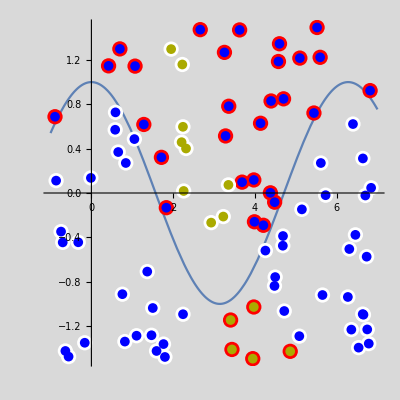
-Graphics-Error: 4.49785

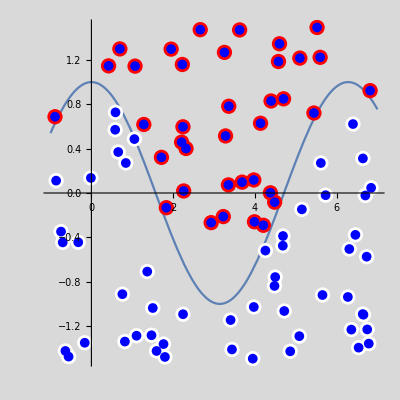
-Graphics-Error: 5.63399

{4,3,3,5,3,4,3,3,4,3,4,5,5,4,3,4,4,3,4,3,3,3,4,3,4,4,4,4,3,3,3,4,3,4,3,4,4,4,4,4}

```mathematica
popClassTest[["individuals",All,"fitness"]]
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["individuals",3]]]]
popClassTest[["individuals",All,"total"]]
```

#### Evolving

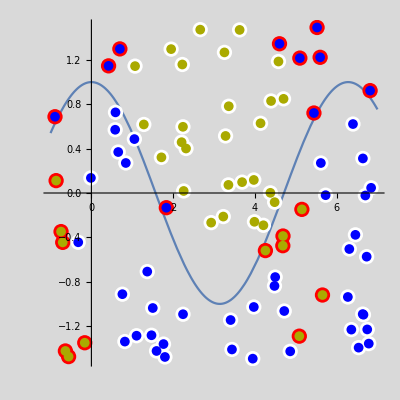
-Graphics-Error: 4.10149

```mathematica
Monitor[
Do[kmEvolveOne[popClassTest,fitnessClassTest],{i,700}];
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
,
kmShowPredictions[classTest,kmClassificationPredictions[classTest,popClassTest[["best"]]]]
]
```

```mathematica
Dynamic[popClassTest["history"]//Length]
Dynamic@popClassTest["state"]
Dynamic@popClassTest["best"]
```